1.1+1.95 x-0.15 x^2

3.9815

0.99

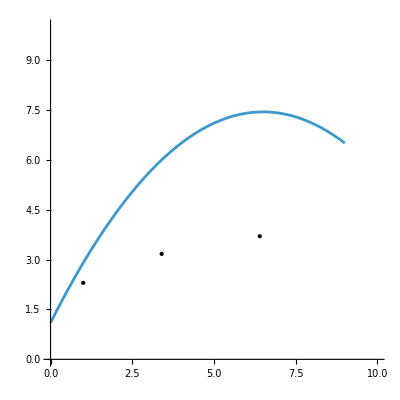

```mathematica
f[x_]:=-0.6*(x/2+0.5)(x/2-7)-1
f[x]//Expand
f[1.7]
f'[3.2]
Show[
ParametricPlot[{
{x,f[x]}
},{x,0,9}, PlotRange->{0,10}], 
Graphics[{Point[{1,2.3}],
Point[{3.4,3.17}],
Point[{6.4, 3.7}]}]
]
```

```mathematica
{2x,f[0.5]+(x-0.5)*f'[0.5]}/.{x->0}
{2x,f[0.5]+(x-0.5)*f'[0.5]}/.{x->1}
```

{0,0.5}

{2,2.7}

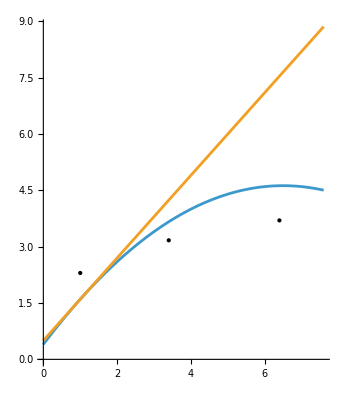

```mathematica
Show[
ParametricPlot[{
{2x,f[x]},
{2x,f[0.5]+(x-0.5)*f'[0.5]}},{x,0,3.8}], 
Graphics[{Point[{1,2.3}],
Point[{3.4,3.17}],
Point[{6.4, 3.7}]}]
]
```

```mathematica
e
```

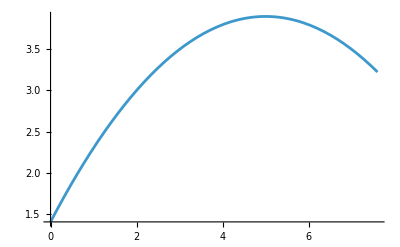

```mathematica
Plot[{f[x/2]},{x,0,2*3.8}]
```

```mathematica
f'[6.4]//Expand
```

-3.12